暴胀阶段只需要考虑场  的能量贡献，于是 Friedmann 方程和场  的运动方程有：
-Graphics-
-Graphics-
为了给出暴胀相，要求状态方程参数 ，等价于动能远小于势能。为了有足够长的时间使得暴胀到可以解释两个疑难的程度，直观上   也应该非常小，于是引入slow-roll parameters 和对应的Slow-roll conditions ：
-Graphics-
当这些条件被破坏 或 ，标志着inflation 阶段解释。

接下来取-Graphics- 的势能形式（Chaotic Inflation）求解：

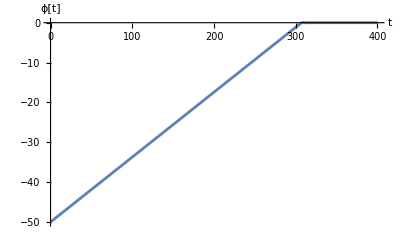

```mathematica
Clear["Global`*"]  
m=1;
T=400;
V[ϕ_]:=1/2 m ϕ^2;
eqn=ϕ''[t]+3 √((8 Pi)/3(1/2 ϕ'[t]^2+V[ϕ[t]]))ϕ'[t]+V'[ϕ[t]]==0;

sol=NDSolve[{eqn,ϕ'[0]==0,ϕ[0]==-50},ϕ[t],{t,0,T}];
Plot[Evaluate[ϕ[t]/.sol],{t,0,400},AxesLabel->{"t","ϕ[t]"}]
```

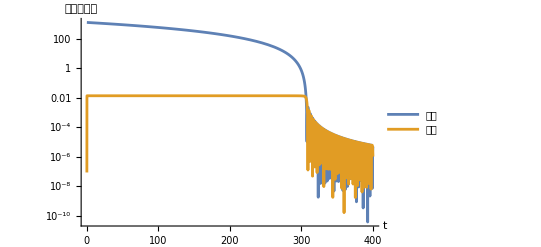

```mathematica
Po=1/2 m (ϕ[t]/. sol)^2;
Ki=1/2 m (D[ϕ[t]/. sol,t])^2;
LogPlot[Evaluate[{Po,Ki}],{t,0,T},AxesLabel->{"t","动能，势能"},PlotLegends->Placed[{"势能","动能"}, {Top,Right}]]
```

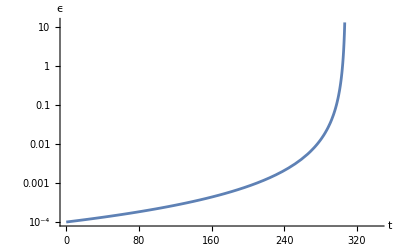

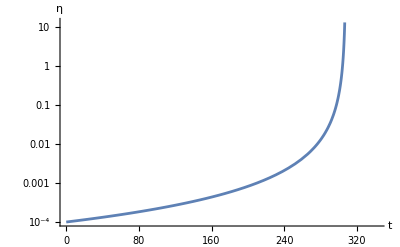

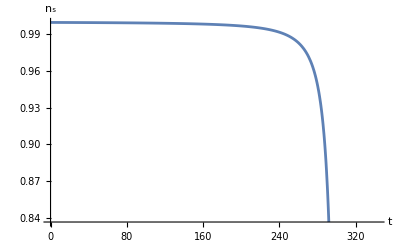

```mathematica
ϵ=1/16(V'[ϕ[t]/. sol]/V[ϕ[t]/. sol])^2;
η=1/8(V''[ϕ[t]/. sol]/V[ϕ[t]/. sol]);
LogPlot[Evaluate[ϵ],{t,0,6/7 T},AxesLabel->{"t","ϵ"}]
LogPlot[Evaluate[η],{t,0,6/7 T},AxesLabel->{"t","η"}]
Plot[Evaluate[1+2η-6ϵ],{t,0,6/7 T},AxesLabel->{"t","n_s"}]
```

```mathematica
eflods[X_]:=NIntegrate[√((8 Pi)/3(1/2(D[ϕ[t]/. sol,t])^2+V[ϕ[t]/. sol])),{t,1,X}]/√((8 Pi)/3(1/2(D[ϕ[t]/. sol,t])^2+V[ϕ[t]/. sol]))/.{t->0};
Plot[eflods[X],{X,1,T}]
```